```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica-nbs"];
Get["ctmc`"]
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 2 binding sites ***)

(*Edge lists and weights*)
edges2={{5,1},{1,5},{2,6},{6,2},{1,2},{1,3},{2,4},{3,1},{3,4},{4,2},{6,5},{5,6}};
weights2={2*c*kboff,kuoff,kuon,2*c*kbon,kon1b,c*kboff,c*kbon,2*kuoff,kon2b,2*kuon,koffu,konu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&kboff>0&&kuon>0&&kbon>0&&kon1b>0&&kuoff>0&&kon2b>0&&koffu>0;
```

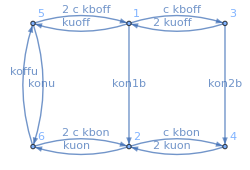

```mathematica
(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{6,5},{2,1},{4,3}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F25 = Fon[[2,5]][[1]];
F45 = Fon[[4,5]][[1]];
F65 = Fon[[6,5]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
offStates = {5,1,3};
onStates = {6,2,4};
F5on = LaplaceTransformToSetByState[Q2,5,onStates,s1];
FoffOn = F5on[[2]][[1]]*F25 +F5on[[3]][[1]]*F45+F5on[[1]][[1]]*F65;
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];

meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt,assum];
```

```mathematica
With[{c=5,kboff=0.05,kuoff=0.2,kbon=0.5,kuon=1,konu=5,koffu=1,kon1b=1,kon2b=1},Evaluate[meanTonLt]]
```

12.4332

```mathematica
expr1=FoffOn/.{konu->0}
expr2=Factor[expr1,Modulus->0];
exprS1=Apart[expr2,s1];  (*treat s2,parameters as constants*)
exprS12=Simplify[Apart[exprS1,s2]]
```

-((8 c^3 kboff^3 koffu kon2b kuon^2)/((-4 c^2 kboff^2 kuoff (-2 c kboff-s1)-2 c kboff (2 c kboff kuoff-(-2 c kboff-s1) (-c kboff-kon1b-kuoff-s1)) (-kon2b-2 kuoff-s1)) (c kbon koffu s2+koffu (kuon+s2) (2 kuon+s2)+s2 (c kbon+kuon+s2) (2 c kbon+2 kuon+s2))))+(4 c^2 kboff^2 koffu kon1b kuon (-kon2b-2 kuoff-s1) (2 kuon+s2))/((-4 c^2 kboff^2 kuoff (-2 c kboff-s1)-2 c kboff (2 c kboff kuoff-(-2 c kboff-s1) (-c kboff-kon1b-kuoff-s1)) (-kon2b-2 kuoff-s1)) (c kbon koffu s2+koffu (kuon+s2) (2 kuon+s2)+s2 (c kbon+kuon+s2) (2 c kbon+2 kuon+s2)))

```mathematica
Pjoint=InverseLaplaceTransform[exprS12,{s1,s2},{t1,t2},Assumptions->assum]
```

```mathematica
d2LogPjoint =D[Log[Pjoint],{c,2}];
integrand = Pjoint *d2LogPjoint
```

```mathematica
(*---------- Method of moments ----------*)

(*Covariance matrix*)
Σx = Simplify[{{varToffLt,covTonToff},{covTonToff,varTonLt}},assum];
```

```mathematica
(*MM estimators*)
cHatOffSym =Simplify[c/.Solve[meanToffLt==sampleToff,c][[1]],assum];
cHatOnSym = Simplify[c/.Solve[meanTonLt==sampleTon,c][[1]],assum];
```

```mathematica
Solve[meanToffLt==sampleToff,c][[1]]
```

```mathematica
cHatOffSym
```

```mathematica
FullSimplify[With[{sampleToff=meanToffLt},Evaluate[cHatOffSym]],assum]
```

```mathematica
(*Jacobian*)
dcHatOff=With[{sampleToff=meanToffLt},Evaluate[D[cHatOffSym, {sampleToff,1}]]];
dcHatOn=With[{sampleTon=meanTonLt},Evaluate[D[cHatOnSym, {sampleTon,1}]]];
delf = {{dcHatOff,0},{0,dcHatOn }};
```

```mathematica
(*Covariance matrix of estimators*)
Σy = delfᵀ.Σx.delf;
```

```mathematica
(*Combined estimator and its variance*)
σ2off = Σy[[1,1]];
σ2on = Σy[[2,2]];
Cov = Σy[[1,2]];

cHat = (cHatOffSym*(σ2on-Cov) + cHatOnSym*(σ2off-Cov))/(σ2off + σ2on - 2Cov);
σ2 = (σ2on*σ2off - Cov^2)/(σ2off + σ2on - 2Cov);

(*Concentration-rescaled Fisher information rates*)
Foff = c^2/ (τ*σ2off);
Fon = c^2/ (τ*σ2on);
Fcomb = c^2/ (τ*σ2);
F[c_,kboff_,kuoff_,kuon_,kbon_,kon1b_,kon2b_,koffu_] := Evaluate[Fcomb];
G[c_,lnkboff_,lnkuoff_,lnkuon_,lnkbon_,lnkon1b_,lnkon2b_,lnkoffu_]:=F[c,Exp[lnkboff],Exp[lnkuoff],Exp[lnkuon],Exp[lnkbon],Exp[lnkon1b],Exp[lnkon2b],Exp[lnkoffu]]
```

```mathematica
(*Maximize*)
lnkmin = -5;
lnkmax = Log[5];
lnkdifflim = Log[0.0888];
cvals = Table[10.^x, {x,Subdivide[-2,4,15]}];
rates = Table[NMaximize[{G[c,lnkboff,lnkuoff,lnkuon,lnkbon,lnkon1b,lnkon2b,lnkoffu]/.{c->x},
lnkmin<lnkboff<lnkdifflim,
lnkmin<lnkuoff<lnkmax,
lnkmin<lnkuon<lnkmax,
lnkmin<lnkbon<lnkdifflim,
lnkmin<lnkon1b<lnkmax,
lnkmin<lnkon2b<lnkmax,
lnkmin<lnkoffu<lnkmax},
{lnkboff,lnkuoff,lnkuon,lnkbon,lnkon1b,lnkon2b,lnkoffu},
Method->"DifferentialEvolution"],{x,cvals}]
```

$Aborted

```mathematica
Test[cval_,lnrates_] := Module[{x1,x2,x3,x4,x5,x6,x7},
{x1,x2,x3,x4,x5,x6,x7} = Table[Exp[r],{r,lnrates}];
With[{c=cval,kboff=x1,kuoff=x2,kuon=x3,kbon=x4,kon1b=x5,kon2b=x6,koffu=x7},
Evaluate[τ]]];
```

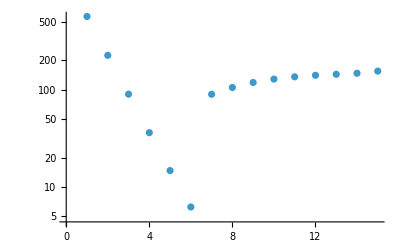

```mathematica
ListPlot[Table[Test[cvals[[k]],Table[rates[[k]][[2]][[i]][[2]],{i,1,7}]],{k,1,15}], ScalingFunctions->"Log"]
```

```mathematica
A = {{a1,0},{0,a4}};
B = {{b1,b2},{b3,b4}};
Aᵀ.B.A
```

{{a1^2 b1,a1 a4 b2},{a1 a4 b3,a4^2 b4}}